```mathematica
diagramf=Import["G:\\calc-online\\gpd\\pic\\1-pic3Dlist-f-n.wdx"];
ff1=Query[1,1]@diagramf;
ff2=Query[2,1]@diagramf;
fg1=Query[1,2]@diagramf;
fg2=Query[2,2]@diagramf;
```

```mathematica
diagramg=Import["G:\\calc-online\\gpd\\pic\\1-pic3Dlist-g-n.wdx"];
gf1=Query[1,1]@diagramg;
gf2=Query[2,1]@diagramg;
gg1=Query[1,2]@diagramg;
gg2=Query[2,2]@diagramg;
```

```mathematica
syff1=Interpolation[Flatten[ff1,1]];
sygf2=Interpolation[Flatten[gf2,1]];
```

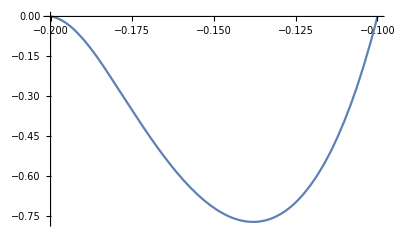

```mathematica
Plot[I*syff1[y,-1],{y,-0.2,-0.1}]
```

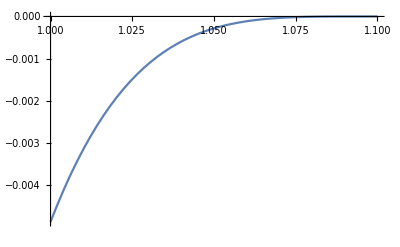

```mathematica
Plot[I*sygf2[x,-1],{x,1,1.1}]
```

```mathematica
syff2=Interpolation[Flatten[ff2,1]];
sygf1=Interpolation[Flatten[gf1,1]];
```

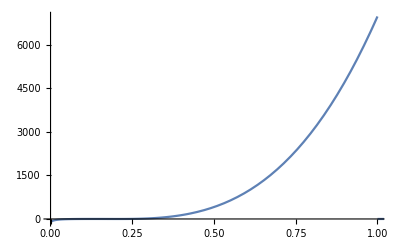

```mathematica
Show[Plot[I*sygf1[x,-1],{x,0,1}],Plot[I*sygf2[x,-1],{x,1,1.1}]]
```

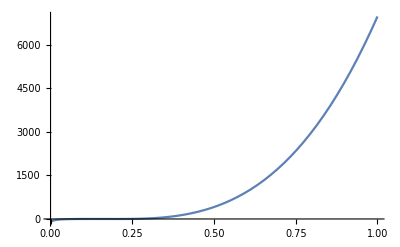

```mathematica
Plot[I*sygf1[x,-1],{x,0,1}]
```

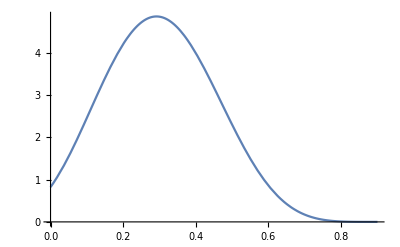

```mathematica
Plot[I*syff2[x,-1],{x,0,0.9}]
```

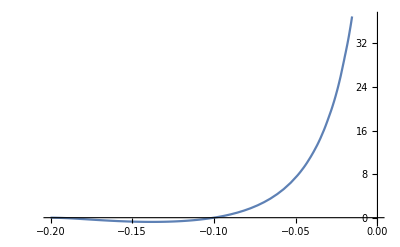

```mathematica
Plot[I*syff1[y,-1],{y,-0.2,0}]
```

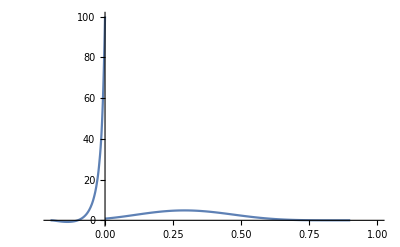

```mathematica
Show[Plot[I*syff1[x,-1],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[I*syff2[x,-1],{x,0,0.9}]]
```

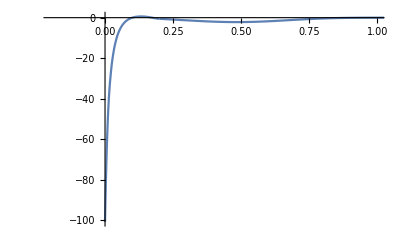

```mathematica
Show[Plot[I*sygf1[x,-1],{x,0,0.2},PlotRange->{{-0.2,1},All}],Plot[I*sygf2[x,-1],{x,0.2,1.1}]]
```

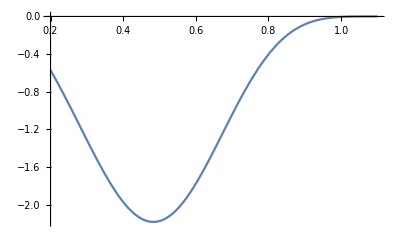

```mathematica
Plot[I*sygf2[x,-1],{x,0.2,1.1}]
```

```mathematica
Plot[I*sygf2[x,-1],{x,1,1.1}]
```

-Graphics-

```mathematica
syfg1=Interpolation[Flatten[fg1,1]];
sygg1=Interpolation[Flatten[gg1,1]];
syfg2=Interpolation[Flatten[fg2,1]];
sygg2=Interpolation[Flatten[gg2,1]];
```

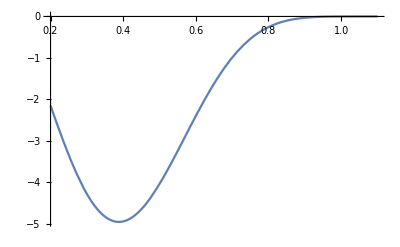

```mathematica
Plot[I*sygg2[x,-1],{x,0.2,1.1}]
```

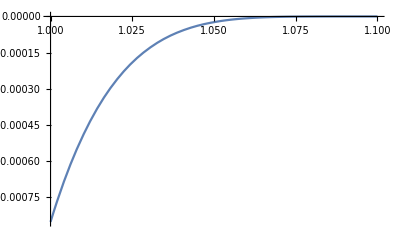

```mathematica
Plot[I*sygg2[x,-1],{x,1,1.1}]
```

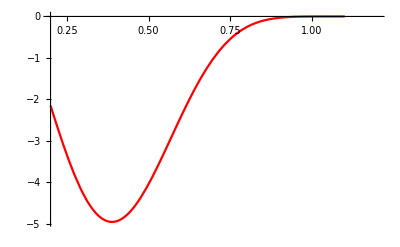
-Graphics-g_gyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*sygg2[x,-1],{x,0.2,1.1},PlotRange->{{0.2,1.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

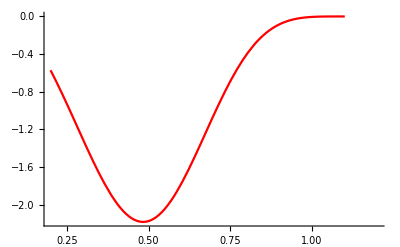
-Graphics-f_gyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*sygf2[x,-1],{x,0.2,1.1},PlotRange->{{0.2,1.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

```mathematica
pathgf2=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-f-test2.pdf"}];
Export[pathgf2,Labeled[Show[Plot[(I)*sygf2[x,-1],{x,0.2,1.1},PlotRange->{{0.2,1.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\g-f-test2.pdf

```mathematica
pathgg2=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-g-test2.pdf"}];
Export[pathgg2,Labeled[Show[Plot[(I)*sygg2[x,-1],{x,0.2,1.1},PlotRange->{{0.2,1.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\g-g-test2.pdf

```mathematica
pathgf20=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-f-test20.pdf"}];
Export[pathgf20,Labeled[Show[Plot[(I)*sygf2[x,-1],{x,1,1.1},PlotRange->{{1,1.1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\g-f-test20.pdf

```mathematica
pathgg20=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-g-test20.pdf"}];
Export[pathgg20,Labeled[Show[Plot[(I)*sygg2[x,-1],{x,1,1.1},PlotRange->{{1,1.1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\g-g-test20.pdf

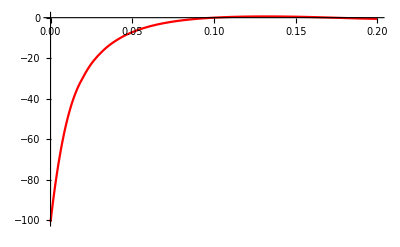
-Graphics-f_gyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*sygf1[x,-1],{x,0,0.2},PlotRange->{{0,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

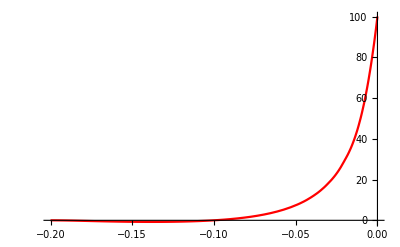
-Graphics-f_fyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*syff1[x,-1],{x,-0.2,0},PlotRange->{{-0.2,0},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

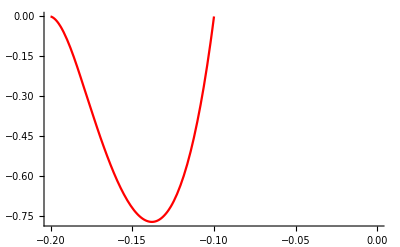
-Graphics-f_fyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*syff1[x,-1],{x,-0.2,-0.1},PlotRange->{{-0.2,0},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

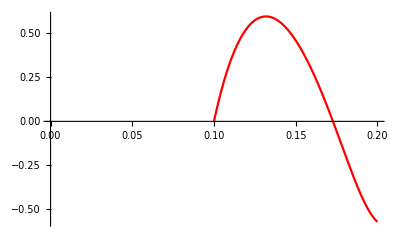
-Graphics-f_gyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*sygf1[x,-1],{x,0.1,0.2},PlotRange->{{0,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

```mathematica
Labeled[Show[Plot[(I)*sygf1[x,-1],{x,0,0.2},PlotRange->{{0,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

-Graphics-f_gyξ=0.1

```mathematica
pathff1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-f-test1.pdf"}];
Export[pathff1,Labeled[Show[Plot[(I)*syff1[x,-1],{x,-0.2,0},PlotRange->{{-0.2,0},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-f-test1.pdf

```mathematica
pathgf1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-f-test1.pdf"}];
Export[pathgf1,Labeled[Show[Plot[(I)*sygf1[x,-1],{x,0,0.2},PlotRange->{{0,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\g-f-test1.pdf

```mathematica
pathfg1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-test1.pdf"}];
Export[pathfg1,Labeled[Show[Plot[(I)*syfg1[x,-1],{x,-0.2,0},PlotRange->{{-0.2,0},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-g-test1.pdf

```mathematica
pathgg1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-g-test1.pdf"}];
Export[pathgg1,Labeled[Show[Plot[(I)*sygg1[x,-1],{x,0,0.2},PlotRange->{{0,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\g-g-test1.pdf

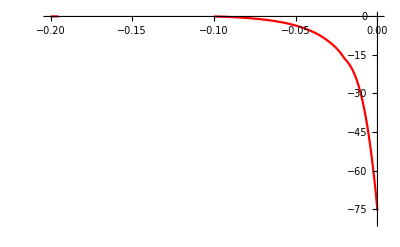
-Graphics-g_fyξ=0.1

```mathematica
Labeled[Show[Plot[(I)*syfg1[x,-1],{x,-0.2,0},PlotRange->{{-0.2,0},{-80,0}},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]
```

```mathematica
pathff10=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-f-test10.pdf"}];
Export[pathff10,Labeled[Show[Plot[(I)*syff1[x,-1],{x,-0.2,-0.1},PlotRange->{{-0.2,-0.1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
pathfg10=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-test10.pdf"}];
Export[pathfg10,Labeled[Show[Plot[(I)*syfg1[x,-1],{x,-0.2,-0.1},PlotRange->{{-0.2,-0.1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
pathgf10=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-f-test10.pdf"}];
Export[pathgf10,Labeled[Show[Plot[(I)*sygf1[x,-1],{x,0.1,0.2},PlotRange->{{0.1,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
pathgg10=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"g-g-test10.pdf"}];
Export[pathgg10,Labeled[Show[Plot[(I)*sygg1[x,-1],{x,0.1,0.2},PlotRange->{{0.1,0.2},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-f-test10.pdf

G:\output\summary\gpd\pic\f-g-test10.pdf

G:\output\summary\gpd\pic\g-f-test10.pdf

G:\output\summary\gpd\pic\g-g-test10.pdf